J1

11/2

J2(λ1)_function

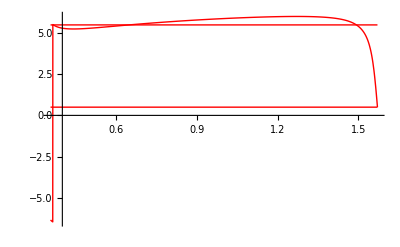

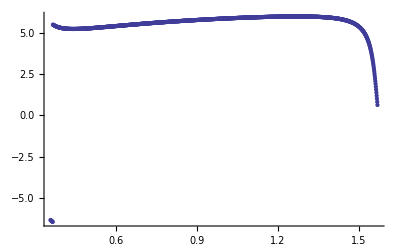

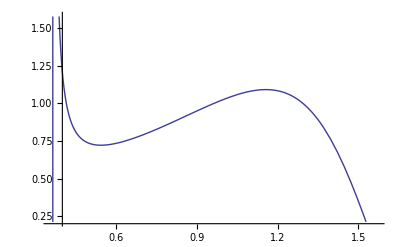

```mathematica
Clear["Global'*"]
NN =12;
ζ = 0.2;

"J1"
J1 = (NN-1)/2


tanλ2ζ[ζ_,λ1_]:=(Tan[λ1]-Tanh[ζ]Tan[NN*ArcTan[Tan[λ1]/Tanh[ζ/2]]-π*J1])/(1+Tanh[ζ]Tan[λ1]Tan[NN*ArcTan[Tan[λ1]/Tanh[ζ/2]]-π*J1])

J2[ζ_,λ1_]:=NN/π ArcTan[tanλ2ζ[ζ,λ1]/Tanh[ζ/2]]-1/π ArcTan[1/Tanh[ζ]((tanλ2ζ[ζ,λ1]-Tan[λ1])/(1+Tan[λ1]tanλ2ζ[ζ,λ1]))]




"J2(λ1)_function"

Plot[{J2[ζ,λ1],1/2,J1},{λ1,ArcTan[Tanh[ζ/2]Tan[π/NN((NN-2)/2)]],π/2},PlotStyle->RGBColor[1,0,0]]



dat=Table[{λ1,J2[ζ,λ1]},{λ1,ArcTan[Tanh[ζ/2]Tan[π/NN((NN-2)/2)]],π/2,1/1000}];
ListPlot[dat,PlotRange->All]


Plot[tanλ2ζ[ζ,λ1],{λ1,ArcTan[Tanh[ζ/2]Tan[π/NN((NN-2)/2)]],π/2}]
```